```mathematica
Quit
```

#### Matching

```mathematica
BB=(A Cos[x]-Z Sin[x])^2//Expand;
WW=(Z Cos[x]+A Sin[x])^2//Expand;
BW=-(A Cos[x]-Z Sin[x])(Z Cos[x]+A Sin[x])//Expand;
```

```mathematica
subs:={Cos[x]->g2/(√(g1^2+g2^2)),Sin[x]->g1/(√(g1^2+g2^2)),g2/g1->Cot[x],g1/g2->Tan[x],(g1^2-g2^2)/(2 g1 g2)->-Cot[2x],(2 g1 g2)/(g1^2-g2^2)->-Tan[2x]};
```

```mathematica
Solve[(g1^2 g2^2)/(g1^2+g2^2)==1/c Coefficient[BB,A,2] g1^2/.subs,c]
Solve[(g1^2 g2^2)/(g1^2+g2^2)== 1/c Coefficient[WW,A,2] g2^2/.subs,c]
Solve[(g1^2 g2^2)/(g1^2+g2^2)== 1/c Coefficient[BW,A,2]g1 g2/.subs,c]
```

{{c→1}}

{{c→1}}

{{c→-1}}

```mathematica
Solve[(2 g1^2 g2^2)/(g1^2+g2^2)== 1/c Coefficient[BB,A Z,1] g1^2/.subs,c]/.subs
Solve[(2 g1^2 g2^2)/(g1^2+g2^2)==1/c Coefficient[WW,A Z,1] g2^2/.subs,c]/.subs
Solve[(2 g1^2 g2^2)/(g1^2+g2^2)==1/c Coefficient[BW,A Z,1]g1 g2/.subs,c]/.subs
```

{{c→-Tan[x]}}

{{c→Cot[x]}}

{{c→-Cot[2 x]}}

#### Running

```mathematica
γWB={{1/2 g1^2-9/2 g2^2+12λ,0,3 g2^2},{0,-3/2 g1^2-5/2 g2^2+12λ,g1^2},{2 g1^2,2 g2^2,-1/2 g1^2+9/2 g2^2+4λ}};
γWB//MatrixForm;
CWB[Λ]={cB[Λ],cW[Λ],cWB[Λ]};
CWB[Λ]//MatrixForm;
```

```mathematica
prod[Λ]=γWB.CWB[Λ];
```

```mathematica
cB[μ]=r[μ]/r[Λ] Collect[CWB[Λ][[1]]-1/(16 π^2)prod[Λ][[1]]Log[Λ/μ],cB[_],Simplify]
cW[μ]=r[μ]/r[Λ] Collect[CWB[Λ][[2]]-1/(16 π^2)prod[Λ][[2]]Log[Λ/μ],cW[_],Simplify]
cWB[μ]=r[μ]/r[Λ] Collect[CWB[Λ][[3]]-1/(16 π^2)prod[Λ][[3]]Log[Λ/μ],cWB[_],Simplify]
```

((-(3 g2^2 cWB[Λ] Log[Λ/μ])/(16 π^2)+cB[Λ] (1-((g1^2-9 g2^2+24 λ) Log[Λ/μ])/(32 π^2))) r[μ])/r[Λ]

((-(g1^2 cWB[Λ] Log[Λ/μ])/(16 π^2)+cW[Λ] (1+((3 g1^2+5 g2^2-24 λ) Log[Λ/μ])/(32 π^2))) r[μ])/r[Λ]

((-((g1^2 cB[Λ]+g2^2 cW[Λ]) Log[Λ/μ])/(8 π^2)+cWB[Λ] (1+((g1^2-9 g2^2-8 λ) Log[Λ/μ])/(32 π^2))) r[μ])/r[Λ]

```mathematica
cB[μ]=Collect[CWB[Λ][[1]]-1/(16 π^2)prod[Λ][[1]]Log[Λ/μ],cB[_],Simplify]
cW[μ]=Collect[CWB[Λ][[2]]-1/(16 π^2)prod[Λ][[2]]Log[Λ/μ],cW[_],Simplify]
cWB[μ]=Collect[CWB[Λ][[3]]-1/(16 π^2)prod[Λ][[3]]Log[Λ/μ],cWB[_],Simplify]
```

-(3 g2^2 cWB[Λ] Log[Λ/μ])/(16 π^2)+cB[Λ] (1-((g1^2-9 g2^2+24 λ) Log[Λ/μ])/(32 π^2))

-(g1^2 cWB[Λ] Log[Λ/μ])/(16 π^2)+cW[Λ] (1+((3 g1^2+5 g2^2-24 λ) Log[Λ/μ])/(32 π^2))

-((g1^2 cB[Λ]+g2^2 cW[Λ]) Log[Λ/μ])/(8 π^2)+cWB[Λ] (1+((g1^2-9 g2^2-8 λ) Log[Λ/μ])/(32 π^2))

#### general C running

```mathematica
Quit
```

```mathematica
Solve[Integrate[1/c,{c,c[μ],c[Λ]},Assumptions->{c[μ]>0,c[Λ]>0}]==Integrate[-γ0/β0 1/g,{g,g[μ],g[Λ]},Assumptions->{g[μ]>0,g[Λ]>0}],c[Λ],Reals]/.g[a_]/g[b_]->((Subscript[α, s][a])/(Subscript[α, s][b]))^(1/2)
```

{{c[Λ]→c[μ] (α_s[Λ]/α_s[μ])^(-γ0/(2 β0))}}

```mathematica
Csol[m_]=DSolveValue[{c'[m]==γ/m g[m]^2 c[m]/.g[m]->1/(√(2β0 Log[m/ΛMS]))},c[m],m]/.Log[a_/b_]->1/2 Log[a^2/b^2]/.Log[n_^2/ΛMS^2]->(4π)/(β0 Subscript[α, s][n]);
Print["c[Λ] = ",Csol[Λ]/Csol[μ]c[μ]//PowerExpand]
```

c[Λ] = c[μ] α_s[Λ]^(-γ/(2 β0)) α_s[μ]^(γ/(2 β0))

#### α_s running

```mathematica
DSolveValue[α'[μ]==-(2 β0)/(4 π μ)α[μ]^2,α[μ],μ]
DSolveValue[{α'[μ]==-(2 β0)/(4 π μ)α[μ]^2,α[ΛMS]==10},α[μ],μ]
```

-(2 π)/(2 π C[1]-β0 Log[μ])

(10 π)/(π-5 β0 Log[ΛMS]+5 β0 Log[μ])

```mathematica
(10 π)/(5 β0 Log[μ/ΛMS])/.Log[a_/b_]->1/2 Log[a^2/b^2]//Simplify
```

(4 π)/(β0 Log[μ^2/ΛMS^2])

#### mass running

```mathematica
Msol[μ_]=DSolveValue[{m'[μ]==-γ/μ g[μ]^2 m[μ]/.g[μ]->1/(√(2β0 Log[μ/ΛMS]))},m[μ],μ]/.Log[a_/b_]->1/2 Log[a^2/b^2]/.Log[n_^2/ΛMS^2]->(4π)/(β0 Subscript[α, s][n]);
Print["M[Λ] = ",Msol[Λ]/Msol[μ]m[μ]//PowerExpand]
```

M[Λ] = m[μ] α_s[Λ]^(γ/(2 β0)) α_s[μ]^(-γ/(2 β0))

```mathematica
DSolveValue[{m'[μ]==-γ/μ g[μ]^2 m[μ]/.g[μ]->1/(√(2β0 Log[μ/ΛMS]))},m[μ],μ]
%/.Log[a_/b_]->1/2 Log[a^2/b^2]/.Log[n_^2/ΛMS^2]->(4π)/(β0 Subscript[α, s][n])
```

C[1] Log[μ/ΛMS]^(-γ/(2 β0))

(2 π)^(-γ/(2 β0)) C[1] (1/(β0 α_s[μ]))^(-γ/(2 β0))

#### r running

```mathematica
Quit
```

```mathematica
Rsol[μ_]=DSolveValue[{r'[μ]==3/(8 π^2 μ)y[μ]^2 r[μ]/.y[μ]->(√2 m[μ])/v/.m[μ]->C Log[μ/ΛMS]^(-γ/(2 β0))},r[μ],μ]
```

ⅇ^((3 C^2 Log[μ/ΛMS]^(1-γ/β0))/(4 π^2 v^2 (1-γ/β0))) C[1]

{{r[μ]→InterpolatingFunction[{{201., 10000.}}, <>][μ]}}

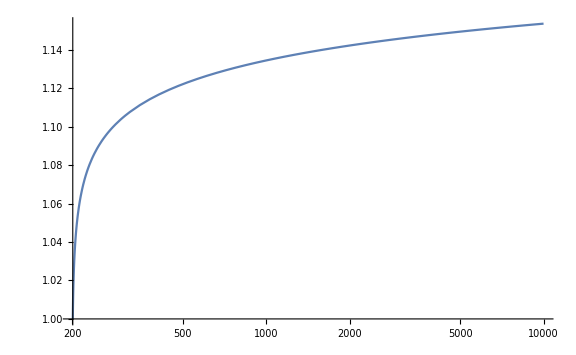

```mathematica
s=NDSolve[{r'[μ]==3/(8 π^2 μ)y[μ]^2 r[μ]/.y[μ]->(√2 m[μ])/v/.m[μ]->C Log[μ/ΛMS]^(-γ/(2 β0))/.{v->246,γ->6*4/3,β0->(11*3-2*5)/3,ΛMS->200,C->125},r[201]==1},r[μ],{μ,201,10000}]
LogLinearPlot[Evaluate[r[μ]/.s],{μ,201,10000},PlotRange->All]
```

#### cγγ

```mathematica
Subscript[c, γγ][μ]=Collect[cB[μ]+cW[μ]-cWB[μ]/.cB[Λ]->cγγ[Λ]-cW[Λ]+cWB[Λ],{r[_],cγγ[Λ],Log[_]},Simplify]
```

((3 g2^2-4 λ) cWB[Λ] Log[Λ/μ])/(8 π^2)+cγγ[Λ] (1+(3 (g1^2+3 g2^2-8 λ) Log[Λ/μ])/(32 π^2))

#### μ_γγ

```mathematica
Subscript[μ, γγ][m_]=1-(4 π^2 v^2 Subscript[c, γγ][m])/(Λ^2 Subscript[i, γ])
```

1-(4 π^2 v^2 c_γγ[m])/(Λ^2 i_γ)

```mathematica
Collect[Subscript[μ, γγ][μ]/.cWB[Λ]->cWB[Subscript[M, H]] r[Λ]/r[μ]/.cWB[Subscript[M, H]]->-(S Λ^2)/(8 π v^2),{r[_],cγγ[Λ],cWB[_]}]/.μ->Subscript[M, H]
```

1+(S (3 g2^2-4 λ) Log[Λ/M_H])/(16 π i_γ)-(4 π^2 v^2 cγγ[Λ] (1+(3 (g1^2+3 g2^2-8 λ) Log[Λ/M_H])/(32 π^2)) r[M_H])/(Λ^2 r[Λ] i_γ)

#### cγZ

```mathematica
Solve[cB==-(cγZ gw)/( g1)+(cW gw^2)/g1^2+cWB (1/2-gw^2/(2 g1^2)),cγZ]//Expand
```

{{cγZ→-(cB g1)/gw+(cWB g1)/(2 gw)+(cW gw)/g1-(cWB gw)/(2 g1)}}

```mathematica
Solve[cγZ==cW g2/g1-cB g1/g2-cWB (g2^2-g1^2)/(2g1 g2),cB]//Expand
```

{{cB→cWB/2-(cγZ g2)/g1+(cW g2^2)/g1^2-(cWB g2^2)/(2 g1^2)}}

```mathematica
Collect[Expand[-(cB[μ] g1)/g2+(cWB[μ] g1)/(2g2)+(cW[μ] g2)/g1-(cWB[μ] g2)/(2g1)]/.cB[Λ]->-(cγZ [Λ]g2)/g1+(cW[Λ] g2^2)/g1^2+cWB[Λ] ((g1^2-g2^2)/(2 g1^2)),{cγZ[Λ],Log[_],cW[_],cWB[_]},Expand]
```

(-(g1 g2)/(8 π^2)+g2^3/(4 g1 π^2)+(g1 λ)/(4 g2 π^2)-(g2 λ)/(4 g1 π^2)) cWB[Λ] Log[Λ/μ]+cγZ[Λ] (1+(g1^2/(32 π^2)+(7 g2^2)/(32 π^2)-(3 λ)/(4 π^2)) Log[Λ/μ])

```mathematica
Collect[Simplify[(-(g1 g2)/(8 π^2)+g2^3/(4 g1 π^2)+(g1 λ)/(4 g2 π^2)-(g2 λ)/(4 g1 π^2)) ]/. 1/(g1 g2)->(2 Cot[2θ])/(g2^2-g1^2),λ,Simplify]
```

(g2^2 (g1^2-2 g2^2) Cot[2 θ])/(4 (g1^2-g2^2) π^2)-(λ Cot[2 θ])/(2 π^2)

```mathematica
Simplify[(g2^2 (2 g1^2-2 g2^2) Cot[2 θ])/(4 (g1^2-g2^2) π^2)]-(λ Cot[2 θ])/(2 π^2)-(g2^2 g1^2 Cot[2 θ])/(4 (g1^2-g2^2) π^2)/. Cot[2θ]/(g1^2-g2^2)->-1/(2 g1 g2)
```

(g1 g2)/(8 π^2)+(g2^2 Cot[2 θ])/(2 π^2)-(λ Cot[2 θ])/(2 π^2)

```mathematica
-16 π^2(g1^2/(32 π^2)+(7 g2^2)/(32 π^2)-(3 λ)/(4 π^2))/.λ->lam/.g2->gw//Expand
-16 π^2(-(g1 g2)/(8 π^2)+g2^3/(4 g1 π^2)+(g1 λ)/(4 g2 π^2)-(g2 λ)/(4 g1 π^2))/.λ->lam/.g2->gw//Expand
```

-g1^2/2-(7 gw^2)/2+12 lam

2 g1 gw-(4 gw^3)/g1-(4 g1 lam)/gw+(4 gw lam)/g1

```mathematica
dtan[x]=b02gw2mb01g12o16π2 tan[x]
```

b02gw2mb01g12o16π2 tan[x]

```mathematica
Collect[D[cW/tan[x]-cB tan[x]-(1-tan[x]^2)/(2tan[x])cWB,x]/.tan'[x]->dtan[x],{b02gw2mb01g12o16π2,cB,cW,cWB},Simplify]/.b02gw2mb01g12o16π2->b02 gw^2-b01 g1^2
```

(-b01 g1^2+b02 gw^2) (-cW/tan[x]-cB tan[x]+(cWB (1+tan[x]^2))/(2 tan[x]))

```mathematica
(cWB (1+tan^2))/(2 tan)/.tan->sin/cos//Simplify
```

(cWB (cos^2+sin^2))/(2 cos sin)

```mathematica
Collect[cgg sin2 +cgz cos2/.sin2->2 sin cos /.cos2 -> cos^2-sin^2/.cgg->cB+cW-cWB/.cgz->cW/tan-cB tan - cWB (1-tan^2)/(2tan)/.tan->sin/cos,{cB,cW,cWB},Simplify]
```

cW (cos^3/sin+cos sin)-(cWB (cos^2+sin^2)^2)/(2 cos sin)+cB (cos sin+sin^3/cos)

### dump

#### old test

```mathematica
prod=γWB.CWB[Λ];
-1/(16 π^2)(prod[[1]]+prod[[2]]-prod[[3]]+2cWB[Λ](3 g2^2-4λ))//Simplify
```

(3 (g1^2+3 g2^2-8 λ) (cB[Λ]+cW[Λ]-cWB[Λ]))/(32 π^2)

```mathematica
-1/(16 π^2)(prod[[2]]*Cot[θ]-prod[[1]]*Tan[θ]-prod[[3]]*Cot[2θ]+2cWB[Λ](g1*g2+4 g2^2 Cot[2θ]-4λCot[2θ]))//FullSimplify
```

1/(32 π^2)(cB[Λ] (-g1^2-9 g2^2+24 λ+2 g1^2 Cot[θ]^2) Tan[θ]+cW[Λ] ((3 g1^2+7 g2^2-24 λ) Cot[θ]-2 g2^2 Tan[θ])+cWB[Λ] (-4 g1 g2-2 g1^2 Cot[θ]-(g1^2+7 g2^2-8 λ) Cot[2 θ]+6 g2^2 Tan[θ]+16 λCot[2 θ]))

#### pokemon

```mathematica
PairedHistogram[EntityValue["Pokemon","Attack"],EntityValue["Pokemon","Defense"],ChartLabels->{"attack","defense"},ChartStyle->{{LightOrange,LightBlue},None}]
```

-Graphics-

```mathematica
stat=EntityValue[Entity["Pokemon",{"Generation"->Entity["PokemonGeneration","GenerationVI"]}],{"Attack","Defense"},"Dataset"];
```

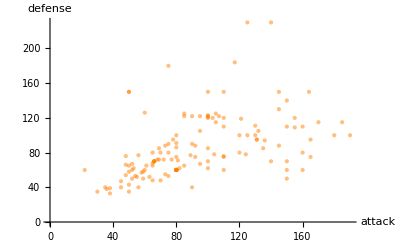

```mathematica
ListPlot[stat,PlotStyle->Directive[Opacity[0.5],Orange,PointSize[Medium]],AxesLabel->Automatic,LabelingFunction->None]
```

```mathematica
wg=Normal[GroupBy[Rule@@@EntityValue["Pokemon",{"Generation","Weight"}],First->Last,Mean]]
```

{Generation I→45.7071 kg,Generation II→49.3114 kg,Generation III→65.0731 kg,Generation IV→74.7854 kg,Generation V→56.9778 kg,Generation VI→81.386 kg}

```mathematica
BarChart3D[wg[[All,2]],ChartLegends->wg[[All,1]],ChartStyle->24]
```

-Graphics3D-

```mathematica
yellowMidweights=EntityList[Entity["Pokemon",{"PokedexColor"->"Red","Weight"->Between[{Quantity[5,"Kilograms"],Quantity[100,"Kilograms"]}]}]]
```

{Charmander,Charmeleon,Charizard,Vileplume,Paras,Parasect,Krabby,Kingler,Voltorb,Electrode,Goldeen,Seaking,Jynx,Magmar,Magikarp,Flareon,Ledyba,Ledian,Ariados,Yanma,Slugma,Magcargo,Octillery,Delibird,Porygon2,Magby,Combusken,Blaziken,Mega Blaziken,Medicham,Mega Medicham,Carvanha,Corphish,Crawdaunt,Latias,Mega Latias,Deoxys (Attack Forme),Deoxys (Defense Forme),Deoxys (Normal Forme),Deoxys (Speed Forme),Kricketune,Magmortar,Porygon-Z,Tepig,Pignite,Pansear,Simisear,Throh,Venipede,Krookodile,Darumaka,Dwebble,Scrafty,Shelmet,Accelgor,Pawniard,Bisharp,Braviary,Heatmor,Fennekin,Fletchinder,Talonflame,Torracat,Incineroar,Tapu Bulu}

```mathematica
ImageCollage[Rule@@@EntityValue[yellowMidweights,{"Weight","Image"}],Background->White]
```

-Graphics-